# Math 350 - Lecture 1

Corresponding to Chapters 1 and 2 in Hazrat

# Mathematica as a Calculator

```mathematica
5*3+2
```

17

```mathematica
%
```

17

```mathematica
Out[2]
```

17

```mathematica
2^9940
```

17304414124542560762148019788370665836131433445011927389524464172250311040491705723218218777207685376683224337381752509320735354666186985304188345202114632894823996854880179234776159522742455025152074904909270141753579841781116470984029881140667272369860424630452427596385313027455896795194530397990581919360716497139381816547688719097422433235562483842899444086106016500410734842232478073498597063460642168103231656929768788600231221014532340663043779128744235244692121994635118442489321531546502211469801685005273297693151004536521972241101279548703350298665285399753916481565469369942540099208129317597261456521281468339929793747860515586873898209447530350970858753000968576215016181815967132899258118023725604544932353715390181149153519096722743246878323995902129387787486916951657867541445514696179676379308592509971277417335930537274386219940364803122455970033340056411912047908229130880930873302017401028233411571859127746392389690495874790127631661663268228871947075424476984951409265028935438114664901669142867709614129511084801332766105417394801025843273005733368990653028123740027535859125166868751133653672089256475369297165342170401349114481993281366298587686043647824536415144874885679165433975754355429608371609261459405835318724248249274547215270638722039703994769928734726386066083290442877180238704421456663646474348448748070807459869922716417947162236800693804821875257349607516341872263535859342045916085474184698140030592296873071794534405595126550936797659578053659598035575299244035013544352921374802601531597095583461053088078804683620974080312994516063992374040537662191316046956898222332850300695639180161501133717147597162803640330630059689359702575748777593774626067132197322981926982456654848888266664700911079001591444639036184301064491355153309057559482065946828922700148430006210195688482335091991797477056242282798656230368899388546035853355412251853728610077507949795883122478884003401241488336960196497705082112388222835611074901828963854206462777771408522786215423194994064980259613656993645600451030441030366881037946149736833202948713517905893439937847157539327210027801734812654699826977966155233215019573232902726482507020009711948776337767384124312315975715746594085452986294390055925140595279536838885593716407044339337143151054137574629238550648225916825989858687585450252836822982348177665684909648000133694791644649563369172863490162999477998750588332100521444273042849723221417097616474393744205297875098719393176559602105427902346230291266916483885973455729950960662492484405010594984142470665786582028152362740434460911721269099795191926206393420416739805709985050896489177826825377664569149327123112673413603751803370372978479063691874358912959263736582485291047590656452759621355140286511572777396814249505254648027924856188989492460919998518707948837077415354314572742362268362286311225065739996340842155232224719511125252429625417380947394444776263949200494098100007434287820116568254572814063595677429137541953945734989509713112441894731776

```mathematica
PrimeQ[2^9940 -1]
```

False

```mathematica
22/7
```

22/7

```mathematica
N[22/7]
```

3.14286

```mathematica
Tan[3 Pi/11] + 4 Sin[2 Pi/11]
```

Cot[(5 π)/22]+4 Sin[(2 π)/11]

```mathematica
Simplify[Out[10]]
```

Cot[(5 π)/22]+4 Sin[(2 π)/11]

```mathematica
FullSimplify[Out[10]]
```

√11

# Numbers

```mathematica
4!
```

24

```mathematica
FactorInteger[24]
```

{{2,3},{3,1}}

```mathematica
2 2 2 3
```

24

```mathematica
PrimeQ[24]
```

False

```mathematica
?Prime
```

```mathematica
Prime[1]
```

2

```mathematica
Prime[10]
```

29

```mathematica
Mod[13,6]
```

1

```mathematica
Binomial[10, 2]
```

45

# Algebraic Computations

```mathematica
(1+x)^4
```

(1+x)^4

```mathematica
Expand[(1+x)^4]
```

1+4 x+6 x^2+4 x^3+x^4

```mathematica
Factor[1 + 3x^3 + 3 x^6  + x^9]
```

(1+x)^3 (1-x+x^2)^3

```mathematica
Apart[(x+2)/((x+3)^2(x^2 + 1))]
```

-1/(10 (3+x)^2)+1/(25 (3+x))+(11-2 x)/(50 (1+x^2))

# Variables

```mathematica
s = 2
```

2

```mathematica
t = 3;
```

```mathematica
t
```

3

```mathematica
Expand[(1+t)^3]
```

1+3 t+3 t^2+t^3

```mathematica
Clear[t]
```

# Equalities

Variable assignment (=)

```mathematica
t= 3;
```

```mathematica
t
```

3

Boolean comparison (==)

```mathematica
t == 3
```

True

```mathematica
t==4
```

False

Delayed assignment (:=)

```mathematica
Random[]
```

0.987531

```mathematica
x = Random[]
```

0.182751

```mathematica
x
```

0.182751

```mathematica
x
```

0.182751

```mathematica
x
```

0.182751

```mathematica
x:=Random[]
```

```mathematica
x
```

0.165431

```mathematica
x
```

0.334262

```mathematica
x
```

0.0410335

# Dynamic Variables

```mathematica
Manipulate[Expand[(1+x)^n], {n, 1, 10, 1}]
```

```mathematica
Manipulate[Plot[a+ c x^2, {x, 0, 4}],{a,-4,4}, {c, -3,3}]
```

# Formulas as functions

```mathematica
f[n_]:=n^3 - 2n +3
```

```mathematica
f[3]
```

24

```mathematica
f[4]
```

59

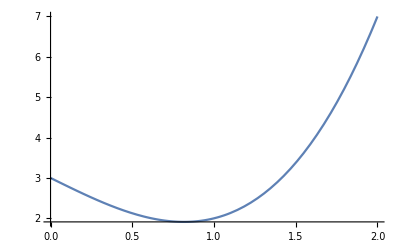

```mathematica
Plot[f[x], {x, 0,2}]
```

```mathematica
f[f[x]]
```

3-2 (3-2 x+x^3)+(3-2 x+x^3)^3

```mathematica
Expand[f[f[f[x]]]]
```

13779-86300 x+242136 x^2-354858 x^3+178776 x^4+301140 x^5-643626 x^6+400470 x^7+225288 x^8-547977 x^9+278136 x^10+158448 x^11-269469 x^12+81012 x^13+80676 x^14-74418 x^15+4428 x^16+22680 x^17-9945 x^18-2436 x^19+3024 x^20-354 x^21-432 x^22+144 x^23+27 x^24-18 x^25+x^27

```mathematica
f[x_]:= Sin[x] Cos[x] + Tan[x]
```

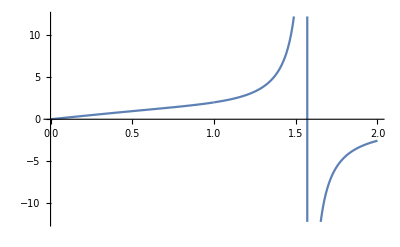

```mathematica
Plot[f[x],{x,0,2}]
```

# What did we do

Arithemetic +, -, /, *, !
Expand, Factor, Apart, Together
= , ==, :=
Boolean functions (PrimeQ)
Formulas into functions
Manipulate 
(Check HW 1 pdf for the first week’s functions to learn)
HW from Ch1 and Ch 2.1